## Initializations

Conditions on the parameters

```mathematica
assumpts={n>1&&d>2&&μ>0&&μ<1&&m>0&&m<1&&b>0&&c>0&&b>c};
```

Fullsimplify with conditions on the parameters

```mathematica
AF[x_]:=Assuming[assumpts,FullSimplify[x]]
```

### Q identity by descent

```mathematica
QinM=-((-1+μ) (μ-d μ+m (-1+d μ)))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ));
QoutM=(m (-1+μ))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ));
QinWF=(-d+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2));
QoutWF=(-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2));
```

```mathematica
R2M=(Qin-Qout)/(1-Qout)/.{Qin->QinM,Qout->QoutM};
R2WF=(Qin-Qout)/(1-Qout)/.{Qin->QinWF,Qout->QoutWF};
```

## DB

```mathematica
Kc b + Kc (-c)(n-1)+Kc b (n-2)//Simplify
```

(b-c) Kc (-1+n)

```mathematica
CDB=-(-c + Kc (-c) + b Kcin )/.{Kc->-((1-m)^2/n+m^2/(n d-n)),Kcin->-((1-m)^2/n+m^2/(n d -n))};
BDB=(b + Kc b + Kcin (-c)(n-1)+Kcin b (n-2))/.{Kc->-((1-m)^2/n+m^2/(n d-n)),Kcin->-((1-m)^2/n+m^2/(n d -n))};
```

```mathematica
XX=(1-Qout)(-c + Kc (-c) + b Kcin )+ (Qin-Qout)(b + Kc b + Kcin (-c)(n-1)+Kcin b (n-2))/.{Kc->-((1-m)^2/n+m^2/(n d-n)),Kcin->-((1-m)^2/n+m^2/(n d -n))}
```

(-c+b (-(1-m)^2/n-m^2/(-n+d n))-c (-(1-m)^2/n-m^2/(-n+d n))) (1-Qout)+(b+b (-(1-m)^2/n-m^2/(-n+d n))+b (-2+n) (-(1-m)^2/n-m^2/(-n+d n))-c (-1+n) (-(1-m)^2/n-m^2/(-n+d n))) (Qin-Qout)

```mathematica
BH=(b + Kc b + Kcin (-c)(n-1)+Kcin b (n-2))/.Kcin->Kc/.{Kc->-((1-m)^2/n+m^2/(n d-n))}//FullSimplify
CH=-(-c + Kc (-c) + b Kcin )/.Kcin->Kc/.{Kc->-((1-m)^2/n+m^2/(n d-n))}//FullSimplify
```

(c (-1+d (-1+m)^2+2 m) (-1+n)+b (-1+2 m+d (1-(-2+m) m (-1+n))-2 m n))/((-1+d) n)

c+((b-c) (-1+d (-1+m)^2+2 m))/((-1+d) n)

```mathematica
prms={b->15,c->1,d->15,n->4}
```

{b→15,c→1,d→15,n→4}

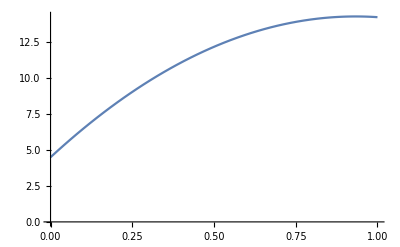

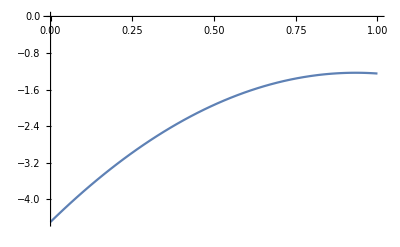

```mathematica
Plot[BH/.prms,{m,0,1},AxesOrigin->{0,0}]
Plot[-CH/.prms,{m,0,1},AxesOrigin->{0,0}]
```

```mathematica
R2M//FullSimplify
rrr=Limit[R2M,d->∞]//FullSimplify
Factor[Numerator[rrr]]
FullSimplify[Denominator[rrr]]
```

-((1+d (-1+m)) (-1+μ))/(1+(-1+n) μ+d (-1+m (-1+n) (-1+μ)+μ-n μ))

(-1+m+μ-m μ)/(-1+m (-1+n) (-1+μ)+μ-n μ)

-(-1+m) (-1+μ)

-1+m (-1+n) (-1+μ)+μ-n μ

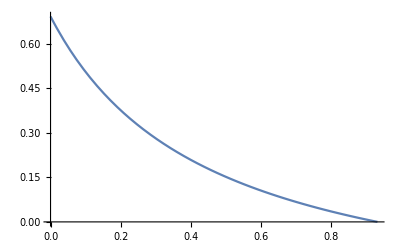

```mathematica
Plot[R2M/.prms/.μ->0.1,{m,0,(d-1)/d/.prms},AxesOrigin->{0,0}]
```

```mathematica
D[R2M,m]//FullSimplify
D[R2WF,m]//FullSimplify
Solve[%==0,m]
```

((-1+d) d n (-1+μ))/(1+(-1+n) μ+d (-1+m (-1+n) (-1+μ)+μ-n μ))^2

(2 (-1+d)^2 d (1+d (-1+m)) n (-1+μ)^2)/((-1+d (2 (1+m (-1+n))+d (-1+(-2+m) m (-1+n)))+2 μ-2 (d (2+d (-1+m)) (-1+m) (-1+n)+n) μ+(1+d (-1+m))^2 (-1+n) μ^2)^2)

{{m→(-1+d)/d}}

```mathematica
Collect[XX,{b,c},FullSimplify]
```

(c (-1+n+Qin-n Qin+2 m (1+(-1+n) Qin-n Qout)+d ((-1+n) (-1+Qin)+m^2 (1+(-1+n) Qin-n Qout)+2 m (-1+Qin-n Qin+n Qout))))/((-1+d) n)+(b (1-Qin+2 m (-1+Qin-n Qin+n Qout)+d (-1+Qin+(-2+m) m (-1+Qin-n Qin+n Qout))))/((-1+d) n)

```mathematica
Assuming[c>0,FullSimplify[(XX/.b->0)/-c/.Qout->0]]
```

-(-1+d+2 m-2 d m+d m^2+n-d n+(-1+d (-1+m)^2+2 m) (-1+n) Qin)/((-1+d) n)

```mathematica
β=Qin-(1/n+((n-1)Qin)/n)((1-m)^2+m^2/(d -1))-Qout (2m(1-m)+(d-2)m^2/(d-1))
```

Qin-((1-m)^2+m^2/(-1+d)) (1/n+((-1+n) Qin)/n)-(2 (1-m) m+((-2+d) m^2)/(-1+d)) Qout

```mathematica
bb=Assuming[c>0,FullSimplify[(XX/.c->0)/b]]//FullSimplify
```

(1-Qin+2 m (-1+Qin-n Qin+n Qout)+d (-1+Qin+(-2+m) m (-1+Qin-n Qin+n Qout)))/((-1+d) n)

```mathematica
bb-β//FullSimplify
```

0

```mathematica
γ=1+-(1/n+((n-1)Qin)/n)((1-m)^2+m^2/(d -1))-Qout (2m(1-m)+(d-2)m^2/(d-1))
```

1+((1-m)^2+m^2/(-1+d)) (-1/n-((-1+n) Qin)/n)-(2 (1-m) m+((-2+d) m^2)/(-1+d)) Qout

```mathematica
cc=Assuming[c>0,FullSimplify[(XX/.b->0)/-c]]
```

((-1+n) (-1+Qin)+2 m (-1+Qin-n Qin+n Qout)+d (-1+n+Qin-n Qin+2 m (1+(-1+n) Qin-n Qout)+m^2 (-1+Qin-n Qin+n Qout)))/((-1+d) n)

```mathematica
cc-γ//FullSimplify
```

0

```mathematica
D[BH,m]//FullSimplify
Solve[%==0]

D[CH,m]//FullSimplify
Solve[%==0]
```

-(2 (b-c) (1+d (-1+m)) (-1+n))/((-1+d) n)

{{c→b},{m→(-1+d)/d},{n→1}}

((b-c) (2+2 d (-1+m)))/((-1+d) n)

{{c→b},{m→(-1+d)/d}}

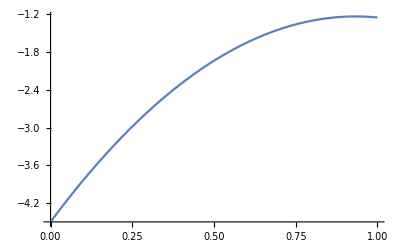

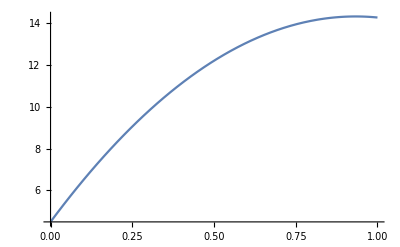

```mathematica
Plot[-CH/.{b->15,c->1,d->15,n->4},{m,0,1}]
Plot[BH/.{b->15,c->1,d->15,n->4},{m,0,1}]
```

## BD

```mathematica
XX=n d(1-Qout)(-c(μ/(n d)^2+1/(n d)(1-μ-din))+b(μ/(n d)^2+1/(n d)(-din)))+n d (n-1)(b μ/(n d)^2-b din/(n d)+b/(n d (n-1))(1-μ)+(μ/(n d)^2+1/(n d)(-din))(-c))(Qin-Qout)//FullSimplify
```

(b (d n (din (-1+Qin-n Qin+n Qout)-(Qin-Qout) (-1+μ))+(1+(-1+n) Qin-n Qout) μ)+c ((-1+Qin-n Qin+n Qout) μ+d n (-1+Qout+din (1+(-1+n) Qin-n Qout)+μ-Qout μ)))/(d n)

#### β

```mathematica
βBDD=(1-μ)(eself+(n-1)ein Qin + (n d-n)eout Qout);
```

```mathematica
βBDI=dself eself + (n-1)din ein+(n d -n )dout eout(*
*)+ (n-1)(din eself + dself ein +(n-2)din ein + (n d -n)dout eout)Qin (*
*)+(n d - n)(dself eout + (n-1)din eout + dout eself+(n-1)dout ein+(n d -2n)dout eout)Qout(*
*)-μ/(n d)(1+(n-1)Qin+(n d -n)Qout)(eself+(n-1)ein+(n d-n)eout);
```

#### γ

```mathematica
γBDD=1-μ;
```

```mathematica
γBDI=dself+(n-1)din Qin+(n d-n)dout Qout-μ/(n d)(1+(n-1)Qin+(n d-n)Qout);
```

```mathematica
β=βBDD-βBDI/.{eout->0,ein->1/(n-1),eself->0,dout->(1-n din)/(n d -n),dself->din}//FullSimplify
γ=γBDD-γBDI/.{eout->0,ein->1/(n-1),eself->0,dout->(1-n din)/(n d -n),dself->din}//FullSimplify
```

(d n (din (-1+Qin-n Qin+n Qout)-(Qin-Qout) (-1+μ))+(1+(-1+n) Qin-n Qout) μ)/(d n)

((1+(-1+n) Qin-n Qout) μ-d n (-1+Qout+din (1+(-1+n) Qin-n Qout)+μ-Qout μ))/(d n)

```mathematica
(β - (XX/.c->0))/b//FullSimplify
```

((-1+b) (d n (din (1+(-1+n) Qin-n Qout)+(Qin-Qout) (-1+μ))+(-1+Qin-n Qin+n Qout) μ))/(b d n)

```mathematica
Collect[β,{Qin,Qout},FullSimplify]
```

-din+μ/(d n)+Qout (-1+din n+μ-μ/d)+Qin (1+din-din n+((-1+n-d n) μ)/(d n))

```mathematica
Collect[(XX/.c->0)/b,{Qin,Qout},FullSimplify]
```

-din+μ/(d n)+Qout (-1+din n+μ-μ/d)+Qin (1+din-din n+((-1+n-d n) μ)/(d n))

```mathematica
FullSimplify[(-2 (-1+n) μ+d n (-1+2 din (-1+n)+μ))/(d^2 (-1+n) n^2)//Expand]
```

(-2 (-1+n) μ+d n (-1+2 din (-1+n)+μ))/(d^2 (-1+n) n^2)

```mathematica
dWfo=(1-μ)(1/(n d)-1/(n d)^2)-(din/(n d)- 1/(n d)^2);
dWfin=(1-μ)(-1/(n d)^2)-(din/(n d)-1/(n d)^2);

dWself=-c dWfo+b dWfin;
dWin=b/(n-1)dWfo-c dWfin+b(n-2)/(n-1)dWfin;
```

```mathematica
X2=dWself(1-Qout)+dWin (Qin-Qout)(n-1)//FullSimplify
```

(b (d n (din (-1+Qin-n Qin+n Qout)-(Qin-Qout) (-1+μ))+(1+(-1+n) Qin-n Qout) μ)+c ((-1+Qin-n Qin+n Qout) μ+d n (-1+Qout+din (1+(-1+n) Qin-n Qout)+μ-Qout μ)))/(d^2 n^2)

```mathematica
(β - (n d X2/.c->0))/b//FullSimplify
```

((-1+b) (d n (din (1+(-1+n) Qin-n Qout)+(Qin-Qout) (-1+μ))+(-1+Qin-n Qin+n Qout) μ))/(b d n)

```mathematica
t1=Collect[β,{Qin,Qout},FullSimplify]
t2=Collect[(n d X2/.c->0)/b,{Qin,Qout},FullSimplify]
t1-t2
```

-din+μ/(d n)+Qout (-1+din n+μ-μ/d)+Qin (1+din-din n+((-1+n-d n) μ)/(d n))

-din+μ/(d n)+Qout (-1+din n+μ-μ/d)+Qin (1+din-din n+((-1+n-d n) μ)/(d n))

0

```mathematica
t1=Collect[γ,{Qin,Qout},FullSimplify]
t2=Collect[-(n d X2/.b->0)/c,{Qin,Qout},FullSimplify]
t1-t2
```

1-din+(-1+1/(d n)) μ+Qout (-1+din n+μ-μ/d)+(-1+n) Qin (-din+μ/(d n))

1-din+(-1+1/(d n)) μ+Qout (-1+din n+μ-μ/d)+(-1+n) Qin (-din+μ/(d n))

0

```mathematica
X2
```

(b (d n (din (-1+Qin-n Qin+n Qout)-(Qin-Qout) (-1+μ))+(1+(-1+n) Qin-n Qout) μ)+c ((-1+Qin-n Qin+n Qout) μ+d n (-1+Qout+din (1+(-1+n) Qin-n Qout)+μ-Qout μ)))/(d^2 n^2)

## Decomposing μ

```mathematica
EXDB=(1-μ)/μ(1-ν)ν((1-Qout)(-c + Kc (-c) + b Kcin )+ (Qin-Qout)(b + Kc b + Kcin (-c)(n-1)+Kcin b (n-2)))/.{Kc->-((1-m)^2/n+m^2/(n d-n)),Kcin->-((1-m)^2/n+m^2/(n d -n))}/.{Qin->QinM,Qout->QoutM}//FullSimplify;
```

Decomposition β γ

```mathematica
β=EXDB/b/.c->0//AF
```

-((-1+μ) (m (-2+d-d m)+μ+d (-1+m) μ) (-1+ν) ν)/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

```mathematica
γ=-EXDB/c/.b->0//AF
```

((-1+μ) (m (2+d (-1+m-n))+(1+d (-1+m)) (-1+n) μ) (-1+ν) ν)/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

Rewrite in human form to check the sign of γ (positive)

```mathematica
((1-μ) (m (d (1-m+n)-2)+(d (1-m)-1) (n-1) μ) (1-ν) ν)/((d-1) μ (1+(n-1) μ)+m (1-μ) (1+d (n-1) μ))-γ//AF
```

0

```mathematica
EXDB-(b β-c γ)//AF
```

0

```mathematica
κ=β/γ//AF
```

-(m (-2+d-d m)+μ+d (-1+m) μ)/(m (2+d (-1+m-n))+(1+d (-1+m)) (-1+n) μ)

Rewrite in human form

```mathematica
(m (d(1-m)-2)+μ-d (1-m) μ)/(m (d (1-m+n)-2)+(d (1-m)-1) (n-1) μ)-κ//AF
```

0

```mathematica
D[κ,m]//AF
%/.m->0//AF
```

(-d^2 m^2 n+(2+2 d (-2+m)+d^2 (2+(-2+m) m)) n μ)/(m (2+d (-1+m-n))+(1+d (-1+m)) (-1+n) μ)^2

(2 n)/((-1+n)^2 μ)

```mathematica
Solve[D[κ,m]==0,m]//AF
mc=m/.%⟦1⟧
```

{{m→((-1+d) (μ-√((2-μ) μ)))/(d (-1+μ))},{m→((-1+d) (μ+√(-(-2+μ) μ)))/(d (-1+μ))}}

((-1+d) (μ-√((2-μ) μ)))/(d (-1+μ))

```mathematica
((d-1) (-μ+√((2-μ) μ)))/(d (1-μ))-mc//AF
```

0

```mathematica
Solve[-μ+√((2-μ) μ)==0,μ]
```

{{μ→0},{μ→1}}

```mathematica
Solve[dc==2,μ]//FullSimplify
```

{}

```mathematica
D[β,m]
```

((-1+μ)^2 (m (-2+d-d m)+μ+d (-1+m) μ) (1+d (-1+n) μ) (-1+ν) ν)/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))^2-((-1+μ) (-2+d-2 d m+d μ) (-1+ν) ν)/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

```mathematica
R2M
```

(-(m (-1+μ))/((1-d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))-((-1+μ) (μ-d μ+m (-1+d μ)))/((1-d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ)))/(1-(m (-1+μ))/((1-d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ)))

How does the competition term change with m?

```mathematica
dK=D[-((1-m)^2/n+m^2/(n d-n)),m]//FullSimplify
```

(2+2 d (-1+m))/(n-d n)

Rewrite it in human-readable form

```mathematica
(2 (d(1-m)-1))/(n(d-1))-dK//Simplify
```

0

```mathematica
Solve[dK==0,m]
dK/.m->0//FullSimplify
```

{{m→(-1+d)/d}}

2/n

The derivative is positive until mc=1-1/d, so Kc increases with m -- this means that competition decreases with m.

1 - Qout decreases with m because its derivative is negative.

```mathematica
dQo=D[1-QoutM,m]//FullSimplify
```

((-1+d) (-1+μ) μ (1+(-1+n) μ))/((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2

Qin - Qout decreases with m

```mathematica
D[QinM-QoutM,m]//FullSimplify
```

((-1+d) (-1+μ) μ (1+(-1+d n) μ))/((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2

Let' s rewrite EXDB.
Note that Kc < 0.

```mathematica
Ks={Kc->-((1-m)^2/n+m^2/(n d-n)),Kcin->-((1-m)^2/n+m^2/(n d -n))};
QM={Qin->QinM,Qout->QoutM};
Fact = (1-μ)/μ(1-ν)ν;
Cpri = (1-Qout)(-c );
Csec=(1-Qout)(Kc (b-c));
Bpri = (Qin-Qout)(b);
Bsec=(Qin-Qout)(n-1)(Kc (b-c));
EXDB2=Fact(Cpri+Csec+Bpri+Bsec)/.{Qin->QinM,Qout->QoutM}/.Ks//FullSimplify
```

((-1+μ) ((b-c) (2+d (-1+m)) m+c d m n-(1+d (-1+m)) (b+c (-1+n)) μ) (-1+ν) ν)/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

Let' s separate primary and secondary effects

```mathematica
Bsec+Csec//Simplify
```

(b-c) Kc (1+(-1+n) Qin-n Qout)

```mathematica
Pr = Fact((Qin-Qout)(b)+(1-Qout)(-c ))/.Ks/.QM//FullSimplify
Sc= Fact(Kc (b-c)((n-1)Qin-n Qout+1))/.Ks/.QM//FullSimplify
EXDB3=(Pr+Sc)/.Ks/.QM//FullSimplify
```

-((-1+μ) (c+c d (-1+m-m n)+b (1+d (-1+m)) (-1+μ)+c (1+d (-1+m)) (-1+n) μ) (-1+ν) ν)/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

((b-c) (-1+d (-1+m)^2+2 m) (-1+μ) (-1+ν) ν)/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

((-1+μ) ((b-c) (2+d (-1+m)) m+c d m n-(1+d (-1+m)) (b+c (-1+n)) μ) (-1+ν) ν)/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

```mathematica
EXDB3-EXDB
```

0

Check how they change with m

```mathematica
DPr=D[Pr,m]//FullSimplify
DSc=D[Sc,m]//FullSimplify
```

((-1+d) (-1+μ)^2 (b+b (-1+d n) μ+c (-1+μ-n μ)) (-1+ν) ν)/((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2

((b-c) (-1+μ) (-1+d-d m^2+(3+d (-4+m (2+m)-n-d (-1+m) (1+m (-1+n)+n))) μ+(2+d (-3+d (-1+m)^2+2 m)) (-1+n) μ^2) (-1+ν) ν)/((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2

Primary effects: constant sign with m,

```mathematica
Solve[DPr==0,m]
```

{}

```mathematica
AF[Reduce[DPr<0,b]]
```

(0<ν<1&&b+c μ+b d n μ>c+b μ+c n μ)||(b+c μ+b d n μ<c+b μ+c n μ&&(ν<0||ν>1))

Primary effects decrease with m.

But how does μ influence this decrease?

```mathematica
DDPr=D[DPr,μ]//AF
```

1/((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^3(-1+d) (-1+μ) ((c-c n+b (-1+d n)) (-1+μ) ((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))+2 (-1+μ) (1-d+m+d m-d m n+2 (1+d (-1+m)) (-1+n) μ) (b+b (-1+d n) μ+c (-1+μ-n μ))+2 ((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ)) (b+b (-1+d n) μ+c (-1+μ-n μ))) (-1+ν) ν

```mathematica
DDPr/.μ->0//FullSimplify
```

-((-1+d) (-(b-c) (2+2 d (-1+m)-m)+(c+b d-2 c d) m n) (-1+ν) ν)/m^3

The derivative with respect to m of the primary effects is negative, and is even lower when μ increases from small.
This is because relatedness decreases with μ.

```mathematica
DDSc=D[DSc,μ]//AF
```

1/((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^3(b-c) (-2 (-1+μ) (-1+d-m-d m+d m n-2 (1+d (-1+m)) (-1+n) μ) (-1+d-d m^2+(3+d (-4+m (2+m)-n-d (-1+m) (1+m (-1+n)+n))) μ+(2+d (-3+d (-1+m)^2+2 m)) (-1+n) μ^2)+(-1+μ) (3+d (-4+m (2+m)-n-d (-1+m) (1+m (-1+n)+n))+2 (2+d (-3+d (-1+m)^2+2 m)) (-1+n) μ) ((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))+(-1+d-d m^2+(3+d (-4+m (2+m)-n-d (-1+m) (1+m (-1+n)+n))) μ+(2+d (-3+d (-1+m)^2+2 m)) (-1+n) μ^2) ((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))) (-1+ν) ν

```mathematica
DDSc/.μ->0//AF
```

-((b-c) (2 (-1+m)+d (4+d (-2-m (-3+n)+m^3 (-1+n))+m (-5+n))) (-1+ν) ν)/m^3

Another thing

```mathematica
BB= (1-μ)/μ(1-ν)ν(b+(n-1)(Kc (b-c)))/.Ks//AF;
CC=-(1-μ)/μ(1-ν)ν(-c+Kc(b-c))/.Ks//AF;
EXDB-((1-QoutM)(BB R2M - CC))//AF
```

0

```mathematica
BCratio=BB/CC//AF
```

(c (-1+d (-1+m)^2+2 m) (-1+n)+b (-1+2 m+d (1-(-2+m) m (-1+n))-2 m n))/((b-c) (-1+d (-1+m)^2+2 m)+c (-1+d) n)

This does not depend on ,μ for this life-cycle.

```mathematica
DBC=D[BCratio,m]//AF
```

-(2 (b-c) (-1+d) (1+d (-1+m)) (b+c (-1+n)) n)/(((b-c) (-1+d (-1+m)^2+2 m)+c (-1+d) n)^2)

```mathematica
(2 (b-c) (d-1) (d (1-m)-1) (b+c (n-1)) n)/(((b-c) (-1+d (-1+m)^2+2 m)+c (-1+d) n)^2)-DBC//AF
```

0

```mathematica
Solve[DBC==0,m]
```

{{m→(-1+d)/d}}

The BC ratio INCREASES with m

```mathematica
D[R2M,m]//AF
```

((-1+d) d n (-1+μ))/(1+(-1+n) μ+d (-1+m (-1+n) (-1+μ)+μ-n μ))^2

```mathematica
D[R2M,μ]//AF
```

((-1+d) (1+d (-1+m)) n)/(1+(-1+n) μ+d (-1+m (-1+n) (-1+μ)+μ-n μ))^2

```mathematica
D[1/R2M,m]//AF
D[%,μ]//AF
```

-((-1+d) d n)/((1+d (-1+m))^2 (-1+μ))

((-1+d) d n)/((1+d (-1+m))^2 (-1+μ)^2)

```mathematica
BCratio
```

(c (-1+d (-1+m)^2+2 m) (-1+n)+b (-1+2 m+d (1-(-2+m) m (-1+n))-2 m n))/((b-c) (-1+d (-1+m)^2+2 m)+c (-1+d) n)

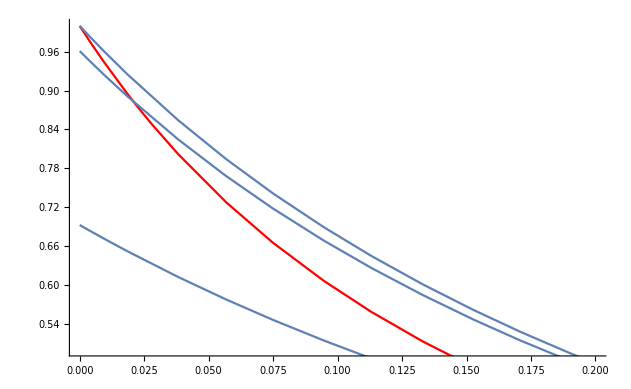

```mathematica
prms={d->15,n->4,b->15,c->1};
theμ=0.01;
Show[Plot[{1/BCratio/.prms},{m,0,(d-1)/d/.prms},PlotStyle->{Red}],Table[Plot[{R2M/.prms/.μ->theμ},{m,0,(d-1)/d/.prms}],{theμ,{0.00000001,0.01,0.1}}],AxesOrigin->{0,0},PlotRange->{{0,0.2},{0.5,1}}]
```

```mathematica
Limit[BCratio,m->0]
Limit[R2M,m->0]
```

1

(1-μ)/(1+(-1+n) μ)

#### Other way of doing it

First take derivatives at m = 0

```mathematica
DPr0=DPr/.m->0//AF
DSc0=DSc/.m->0//AF
```

((-1+μ)^2 (b+b (-1+d n) μ+c (-1+μ-n μ)) (-1+ν) ν)/((-1+d) (μ+(-1+n) μ^2)^2)

((b-c) (-1+μ) (1+μ (-3+d+d n+(-2+d) (-1+n) μ)) (-1+ν) ν)/((-1+d) (μ+(-1+n) μ^2)^2)

Rewrite in human form

```mathematica
-((1-μ)^2 ((b-c)(1-μ)+(b d -c )n μ) (1-ν) ν)/((d-1) (μ+(n-1) μ^2)^2)-DPr0//AF
```

0

```mathematica
((b-c) (1-μ) (1+μ (d(n+1)-3+μ(d-2)(n-1) )) (1-ν) ν)/((d-1) (μ+(n-1) μ^2)^2)-DSc0//AF
```

0

and see that DPr0 is negative while DSc0 is positive :
The primary (positive) effects decrease and the Secondary (negative) effects increase, i.e. get closer to zero, i.e. competition decreases.   
(Note: will have to choose between positive or negative secondary effects).

How do these effects change with μ?

```mathematica
DDPr0=D[DPr0,μ]//AF//Factor
```

-((-1+μ) (-2 b+2 c+5 b μ-5 c μ-4 b n μ+5 c n μ-b d n μ-4 b μ^2+4 c μ^2+5 b n μ^2-7 c n μ^2+2 b d n μ^2+3 c n^2 μ^2-3 b d n^2 μ^2+b μ^3-c μ^3-b n μ^3+2 c n μ^3-b d n μ^3-c n^2 μ^3+b d n^2 μ^3) (-1+ν) ν)/((-1+d) μ^3 (1-μ+n μ)^3)

```mathematica
DDSc0=D[DSc0,μ]//AF
```

-((b-c) (-2-(-8+d+(4+d) n) μ-3 (-1+n) (-4+d+d n) μ^2+(-1+n) (-8+3 d+4 n) μ^3+(-2+d) (-1+n)^2 μ^4) (-1+ν) ν)/((-1+d) (μ+(-1+n) μ^2)^3)

```mathematica
Limit[DPr0,μ->0]
```

((-1+ν) ν DirectedInfinity[b-c])/(-1+d)

```mathematica
Limit[DDPr0,μ->0]
```

((-1+ν) ν DirectedInfinity[-b+c])/(-1+d)

```mathematica
Limit[EXDB,m->0]//FullSimplify
```

-((b+c (-1+n)) (-1+μ) (-1+ν) ν)/(1+(-1+n) μ)

```mathematica
Limit[EXDB,μ->0]//AF
Limit[%,m->0]//AF
```

((b-c) (2+d (-1+m))+c d n) (-1+ν) ν

-(b (-2+d)-c (-2+d+d n)) (-1+ν) ν

## Brouillon

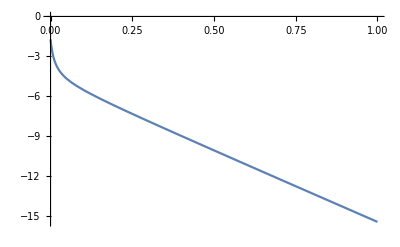

```mathematica
Plot[EXDB/.{b->4,c->1,d->15,n->4,ν->0.45}/.μ->0.001,{m,0,1},AxesOrigin->{0,0}]
```

```mathematica
mzs=Assuming[assumpts,FullSimplify[Solve[NDSc==0,m]]]
```

{}

The denominator is negative, so the admissible solution cannot be the second one.

```mathematica
mz=m/.mzs⟦1⟧//FullSimplify
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

m/.{}⟦1⟧

```mathematica
mzs/.μ->0//FullSimplify
```

{}

When m is small, the derivative is always positive

```mathematica
t0=NDSc/.m->0//FullSimplify
```

NDSc

Let' s quickly check that this is the case

```mathematica
tt=Assuming[assumpts,FullSimplify[Solve[t0==0,μ]]]
```

{}

```mathematica
Solve[(μ/.tt⟦3⟧)==0,d]
(μ/.tt⟦3⟧)/.{d->15,n->4}//N
```

Part::partw: Part 3 of {} does not exist.

ReplaceAll::reps: {{}⟦3⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{}

Part::partw: Part 3 of {} does not exist.

ReplaceAll::reps: {{}⟦3⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

μ/.{}⟦3⟧

When m is small this derivative is always of the same sign for admissible (>0) values of μ.

So we have increasing then decreasing

```mathematica
tt/.{d->5,n->4}//N
```

{}

```mathematica
(√((-1+d) d))/d/.d->15//N
```

0.966092

```mathematica
Denominator[DPr]-Denominator[DSc]
```

0

Primary and secondary effects have the same denominators so we can focus just on their numerators.

```mathematica
NDPr=Numerator[DPr]//FullSimplify
NDSc=Numerator[DSc]//FullSimplify
```

(-1+d) (-1+μ)^2 (b+b (-1+d n) μ+c (-1+μ-n μ)) (-1+ν) ν

(b-c) (-1+μ) (-1+d-d m^2+(3+d (-4+m (2+m)-n-d (-1+m) (1+m (-1+n)+n))) μ+(2+d (-3+d (-1+m)^2+2 m)) (-1+n) μ^2) (-1+ν) ν

```mathematica
Assuming[assumpts,Simplify[Reduce[NDPr<0,b]]]
```

(0<ν<1&&b+c μ+b d n μ>c+b μ+c n μ)||(b+c μ+b d n μ<c+b μ+c n μ&&(ν<0||ν>1))

```mathematica
Assuming[assumpts,Simplify[Reduce[NDSc<0,b]]]
```

$Aborted

```mathematica
EXDB-EXDB2
```

0

```mathematica
Assuming[{m>0&&m<1},FullSimplify[D[-CDB,m]]]
Solve[%==0,m]
Assuming[{m>0&&m<1},FullSimplify[D[BDB,m]]]
```

-(2 (b-c) (1+d (-1+m)))/((-1+d) n)

{{m→(-1+d)/d}}

-(2 (b-c) (1+d (-1+m)) (-1+n))/((-1+d) n)

```mathematica
BDB//FullSimplify
```

(c (-1+d (-1+m)^2+2 m) (-1+n)+b (-1+2 m+d (1-(-2+m) m (-1+n))-2 m n))/((-1+d) n)

```mathematica
Limit[BDB,d->∞]//FullSimplify
```

(b (1-(-2+m) m (-1+n))+c (-1+m)^2 (-1+n))/n

```mathematica
Solve[BDB==0,b]//FullSimplify
```

{{b→(c (-1+d (-1+m)^2+2 m) (-1+n))/(1-d (-1+m)^2+2 m (-1+n)+d (-2+m) m n)}}

```mathematica
EXDB0=Limit[EXDB,μ->0]//FullSimplify
Limit[%,d->∞]
```

((b-c) (2+d (-1+m))+c d n) (-1+ν) ν

(b (-1+m)+c (1-m+n)) (-1+ν) ν ∞

```mathematica
Solve[EXDB0==0,b]//FullSimplify
Limit[b/.%,d->∞]
```

{{b→c-(c d n)/(2+d (-1+m))}}

{(c (-1+m-n))/(-1+m)}

```mathematica
ΔEXDB=EXDB - Limit[EXDB,μ->0]//FullSimplify
```

(b (-2+d-d m)+c (2+d (-1+m-n))+((-1+μ) ((b-c) (2+d (-1+m)) m+c d m n-(1+d (-1+m)) (b+c (-1+n)) μ))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))) (-1+ν) ν

```mathematica
ΔEXDB//Factor
```

-((μ (b-c-2 b d+2 c d+b d^2-c d^2+2 b d m-2 c d m-2 b d^2 m+2 c d^2 m+b d^2 m^2-c d^2 m^2-c n+2 c d n-c d^2 n-2 b d m n+c d m n+b d^2 m n-b d^2 m^2 n+c d^2 m^2 n-c d^2 m n^2-b μ+c μ+2 b d μ-2 c d μ-b d^2 μ+c d^2 μ-2 b d m μ+2 c d m μ+2 b d^2 m μ-2 c d^2 m μ-b d^2 m^2 μ+c d^2 m^2 μ+2 b n μ-c n μ-3 b d n μ+c d n μ+b d^2 n μ+3 b d m n μ-2 c d m n μ-2 b d^2 m n μ+c d^2 m n μ+b d^2 m^2 n μ-c d^2 m^2 n μ+c d n^2 μ-c d^2 n^2 μ+c d^2 m n^2 μ) (-1+ν) ν)/(-m+μ-d μ+m μ+d m μ-d m n μ-μ^2+d μ^2-d m μ^2+n μ^2-d n μ^2+d m n μ^2))

```mathematica
D[EXDB0,m]
```

(b-c) d (-1+ν) ν

```mathematica
D[ΔEXDB,m]//FullSimplify
```

(-b d+c d-((-1+μ)^2 ((b-c) (2+d (-1+m)) m+c d m n-(1+d (-1+m)) (b+c (-1+n)) μ) (1+d (-1+n) μ))/((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2+((-1+μ) (b (2+d (-1+2 m-μ))+c (-2+d (1-2 m+n+μ-n μ))))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))) (-1+ν) ν

```mathematica
EXBD0=EXBD/.μ->0//FullSimplify
```

EXBD

```mathematica
EXBD0
```

EXBD

## Generic

```mathematica
dW=dWs+(n-1)dWi R2;
```

```mathematica
dWs=dWfs (-c)+b dWfi;
dWi=dWfs b/(n-1)+dWfi(-c)+(n-2)/(n-1)b dWfi;
```

```mathematica
dWfsDB=(1-μ)1/(n d)(1-(1-m)^2/n-m^2/(n(d-1)));
dWfiDB=(1-μ)1/(n d)(-(1-m)^2/n-m^2/(n(d-1)));
```

```mathematica
dWfsBD=(1-μ)(1/(n d)-1/(n d)^2)-((1-m)/(n n d)-1/(n d)^2);
dWfiBD=(1-μ)(-1/(n d)^2)-((1-m)/(n n d)-1/(n d)^2);
```

```mathematica
dWfsWF=(1-μ)(1-(1-m)^2/n-m^2/(n(d-1)));
dWfiWF=(1-μ)(-(1-m)^2/n-m^2/(n(d-1)));
```

```mathematica
dWDB=dW/.{dWfs->dWfsDB,dWfi->dWfiDB}
```

(-1+n) R2 (-(c (-(1-m)^2/n-m^2/((-1+d) n)) (1-μ))/(d n)+(b (1-(1-m)^2/n-m^2/((-1+d) n)) (1-μ))/(d (-1+n) n)+(b (-(1-m)^2/n-m^2/((-1+d) n)) (-2+n) (1-μ))/(d (-1+n) n))+(b (-(1-m)^2/n-m^2/((-1+d) n)) (1-μ))/(d n)-(c (1-(1-m)^2/n-m^2/((-1+d) n)) (1-μ))/(d n)

### Check the sign of B

#### Check for BD competition

Competition term in the BD life-cycle

```mathematica
BDcomp=μ/(n d)-(1-m)/n;
```

It increases with m (derivative >0)

```mathematica
D[BDcomp,m]//AF
```

1/n

It is negative when m=0 (because μ<d)

```mathematica
BDcomp/.m->0//AF
```

(-d+μ)/(d n)

And it is still negative when we reach mc

```mathematica
BDcomp/.m->(d-1)/d//AF
```

(-1+μ)/(d n)

#### Check for DB competition

```mathematica
DBcomp = -(1-μ)((1-m)^2/n+m^2/(n (d-1)));
```

```mathematica
dcomp=D[DBcomp,m]//AF
```

(2 (1+d (-1+m)) (-1+μ))/((-1+d) n)

```mathematica
Solve[dcomp==0,m]
```

{{m→(-1+d)/d}}

```mathematica
dcomp/.m->0//AF
```

(2-2 μ)/n

#### DB

```mathematica
BDB=(n-1)dWi/.{dWfi->dWfiDB,dWfs->dWfsDB}//AF
```

((-c (-1+d (-1+m)^2+2 m) (-1+n)+b (1-d (-1+m)^2+2 m (-1+n)+d (-2+m) m n)) (-1+μ))/((-1+d) d n^2)

```mathematica
((-c (1-d (1-m)^2-2 m) (n-1)+b (-1+d (1-m)^2-2 m (n-1)+d (2-m) m n)) (1-μ))/((d-1) d n^2)-BDB//AF
```

0

```mathematica
Solve[BDB==0,b]//AF
bcrit=b/c/.%⟦1⟧;
```

{{b→(c (-1+d (-1+m)^2+2 m) (-1+n))/(1-d (-1+m)^2+2 m (-1+n)+d (-2+m) m n)}}

```mathematica
((d m^2-2 d m +d-1+2 m) (n-1))/(1-d (1-m)^2+2 m (n-1)-d (2-m) m n)-bcrit//AF
```

0

```mathematica
Solve[bcrit==0]//FullSimplify
```

{{d→(1-2 m)/(-1+m)^2},{n→1}}

```mathematica
AF[Reduce[bcrit<0]]
```

True

#### BD

```mathematica
BBD=(n-1)dWi/.{dWfi->dWfiBD,dWfs->dWfsBD}//AF
```

(-c (-1+n) (d (-1+m)+μ)+b ((-1+n) μ+d (1+m (-1+n)-n μ)))/(d^2 n^2)

```mathematica
n d(1-Qout)(-c(μ/(n d)^2+1/(n d)(1-μ-din))+b(μ/(n d)^2+1/(n d)(-din)))+n d (n-1)(b μ/(n d)^2-b din/(n d)+b/(n d (n-1))(1-μ)+(μ/(n d)^2+1/(n d)(-din))(-c))(Qin-Qout)-(1-Qout)*(BBD (Qin-Qout)/(1-Qout)+CBD)/.din->(1-m)/n//AF
```

1/(d^2 n^2)(b d (-(1+m (-1+n)) (Qin-Qout)+d n (-1+Qin+m (1+(-1+n) Qin-n Qout)))+d (CBD d n^2 (-1+Qout)+c ((-1+m) (-1+n) (Qin-Qout)-d n (-1+n+Qin-n Qin+m (1+(-1+n) Qin-n Qout))))-c (-1+d n) ((-1+n) (Qin-Qout)+d n (-1+Qout)) μ+b (Qin-Qout+n (-Qin+Qout-d (-1+(-1+d) n (Qin-Qout)+Qout))) μ)

```mathematica
-CBD//AF
(-c(μ/(n d)^2+1/(n d)(1-μ-din))+b(μ/(n d)^2+1/(n d)(-din)))/.din->(1-m)/n//AF
```

-CBD

(b (d (-1+m)+μ)-c (μ+d (-1+m+n-n μ)))/(d^2 n^2)

```mathematica
(n-1)(b μ/(n d)^2-b din/(n d)+b/(n d (n-1))(1-μ)+(μ/(n d)^2+1/(n d)(-din))(-c))/.din->(1-m)/n//AF
BBD//AF
```

(-c (-1+n) (d (-1+m)+μ)+b ((-1+n) μ+d (1+m (-1+n)-n μ)))/(d^2 n^2)

(-c (-1+n) (d (-1+m)+μ)+b ((-1+n) μ+d (1+m (-1+n)-n μ)))/(d^2 n^2)

```mathematica
Solve[BBD==0,μ]//AF
```

{{μ→(d (b (1+m (-1+n))+c (-1+m+n-m n)))/(b+c (-1+n)+b (-1+d) n)}}

```mathematica
Solve[(d (b (1+m (-1+n))+c (-1+m+n-m n)))/(b+c (-1+n)+b (-1+d) n)==1]
```

{{c→b},{m→(-1+d)/d},{n→1}}

```mathematica
Solve[BBD==0,b]//AF
bcrit=b/c/.%⟦1⟧;
```

{{b→(c (-1+n) (d (-1+m)+μ))/((-1+n) μ+d (1+m (-1+n)-n μ))}}

```mathematica
AF[Reduce[bcrit<0]]
```

(d>d m+μ&&m≥μ)||(m<μ&&d m+μ<d&&(1+m n≥m+n μ||d+d m n+n μ>d m+μ+d n μ))

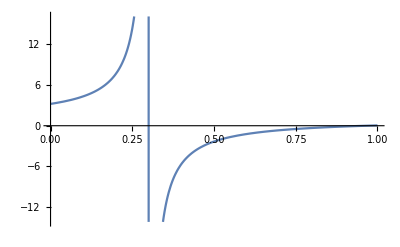

```mathematica
Plot[bcrit/.{n->4,d->15,μ->0.5},{m,0,1}]
```

#### WF

See DB

```mathematica
BWF=(n-1)dWi/.{dWfi->dWfiWF,dWfs->dWfsWF}//AF
```

((-c (-1+d (-1+m)^2+2 m) (-1+n)+b (1-d (-1+m)^2+2 m (-1+n)+d (-2+m) m n)) (-1+μ))/((-1+d) n)

### Compare CB ratio to R

```mathematica
CDB=-dWs/.{dWfi->dWfiDB,dWfs->dWfsDB}//AF
CBD=-dWs/.{dWfi->dWfiBD,dWfs->dWfsBD}//AF
CWF=-dWs/.{dWfi->dWfiWF,dWfs->dWfsWF}//AF
```

-(((b-c) (-1+d (-1+m)^2+2 m)+c (-1+d) n) (-1+μ))/((-1+d) d n^2)

(-b (d (-1+m)+μ)+c (μ+d (-1+m+n-n μ)))/(d^2 n^2)

-(((b-c) (-1+d (-1+m)^2+2 m)+c (-1+d) n) (-1+μ))/((-1+d) n)

#### DB

```mathematica
CDB=-dWs/.{dWfi->dWfiDB,dWfs->dWfsDB}//AF
```

-(((b-c) (-1+d (-1+m)^2+2 m)+c (-1+d) n) (-1+μ))/((-1+d) d n^2)

```mathematica
CBrDB=CDB/BDB//AF
```

-((b-c) (-1+d (-1+m)^2+2 m)+c (-1+d) n)/(-c (-1+d (-1+m)^2+2 m) (-1+n)+b (1-d (-1+m)^2+2 m (-1+n)+d (-2+m) m n))

```mathematica
PlotRC[ratio_,R_,prms_,mulist_]:=Show[Table[Plot[ratio/.prms/.μ->theμ,{m,0,(d-1)/d/.prms},PlotStyle->Red],{theμ,mulist}],Table[Plot[R/.prms/.μ->theμ,{m,0,(d-1)/d/.prms},PlotStyle->Blue],{theμ,mulist}],PlotRange->{{0,0.2},All}]
```

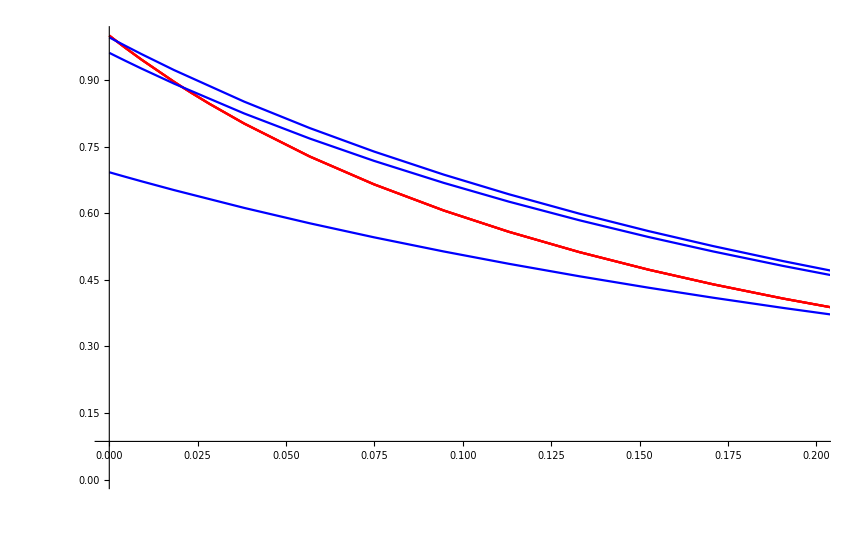

```mathematica
PlotRC[CDB/BDB,R2M,{b->15,c->1,d->15,n->4},{0.001,0.01,0.1}]
```

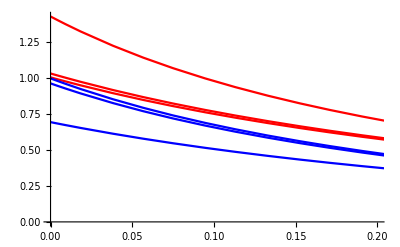

```mathematica
PlotRC[CBD/BBD,R2M,{b->15,c->1,d->15,n->4},{0.001,0.01,0.1}]
```

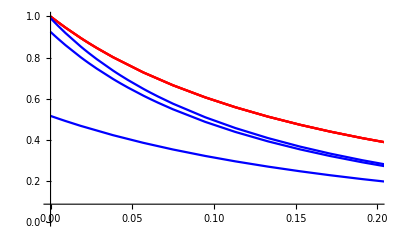

```mathematica
PlotRC[CWF/BWF,R2WF,{b->15,c->1,d->15,n->4},{0.001,0.01,0.1}]
```